```mathematica
ClearAll[files,importfile,raw]
```

```mathematica
files=FileNames["*.xlsx",NotebookDirectory[]]
```

{/Users/leonidbarinov/Desktop/latexlabs/5 семестр (Квантовая физика)/4.2/4.2.xlsx}

```mathematica
importfile=files⟦1⟧
```

/Users/leonidbarinov/Desktop/latexlabs/5 семестр (Квантовая физика)/4.2/4.2.xlsx

```mathematica
raw = Import[importfile];
```

```mathematica
makeAssoc[header_][row_]:=<|header->row//Thread|>;
makeDataset@raw_:=With[{header=raw⟦1⟧,data=raw⟦2;;⟧},
makeAssoc@header/@data
]//Dataset;
```

```mathematica
ClearAll[dataset1,dataset2,dataset1WithErrs,dataset2WithErrs]
```

## Dataset1

```mathematica
dataset1 = makeDataset[raw⟦4⟧]
```

Dataset[<>]

```mathematica
dataset1WithErrs=dataset1[All,<|"J"->(#J&),"N"-> (Around[#N, #dN] &)|>]
```

Dataset[<>]

```mathematica
frame[legend_]:=Framed[legend,FrameStyle->Black,RoundingRadius->10,FrameMargins->0,Background->White]
```

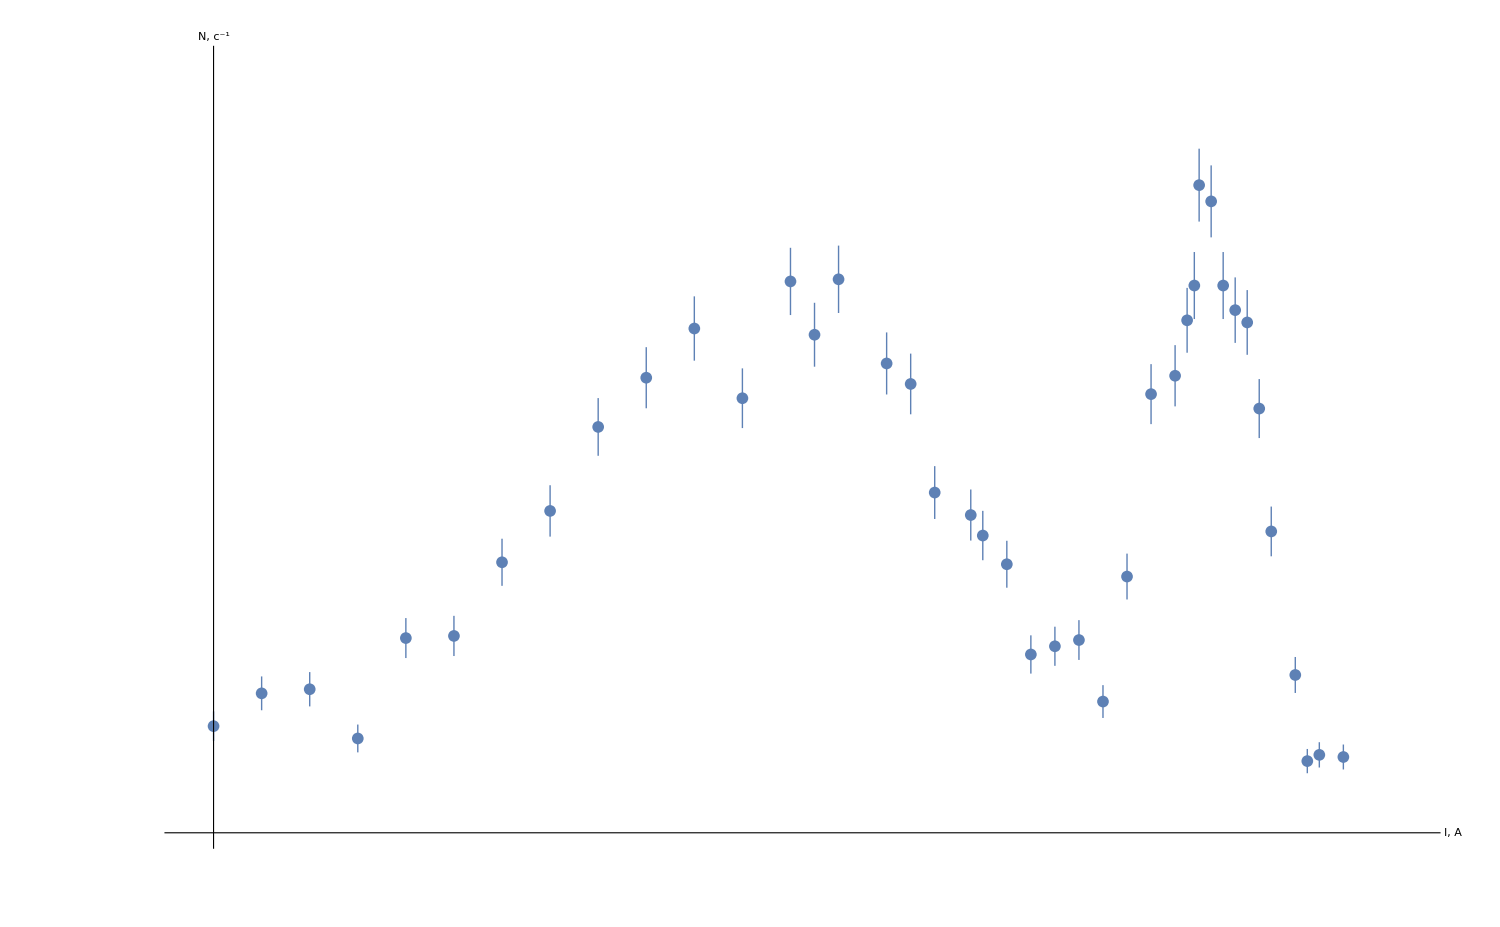

```mathematica
Show[
ListPlot[
{dataset1WithErrs},
PlotRange-> {{-0.1,5},{0, 4.7}},
Ticks-> {Range[-1000,1000, 0.5],Range[-1000,1000, 0.5]},
TicksStyle->Directive[Black, 14],
PlotMarkers-> {Automatic, 12},
AxesLabel-> {Style["I, A", Large], Style["N, c^-1", Large]},
AxesStyle->Directive[Arrowheads[0.02],Black],
ImageSize->1500,
GridLines-> {Range[-1000,1000, 0.05],Range[-1000,1000, 0.1]},
LabelStyle->Black,
PlotLegends->Placed[LineLegend[
Automatic,
{"V_2 = 4 В","V_2 = 6 В", "V_2 = 8 В"},
LegendMarkerSize->15,
LegendFunction->frame,
LabelStyle->{FontSize->18},
LegendLayout->"Column"
],
{Scaled[0.2],Scaled[0.75]}
]
]
]
```

## Dataset4

```mathematica
dataset2 = makeDataset[raw⟦5⟧]
```

Dataset[<>]

```mathematica
datasetline = Sort[raw⟦5⟧⟦2;;⟧]⟦7;;25⟧
```

{{79.7,193.594},{105.9,176.546},{134.9,170.862},{166.2,154.666},{199.6,141.176},{234.7,111.005},{271.4,113.647},{290.3,100.224},{309.4,101.023},{348.6,81.3637},{368.6,74.9536},{388.8,58.6902},{419.5,51.7994},{429.8,48.0198},{450.7,42.1784},{471.7,26.3983},{492.8,26.7644},{514.2,26.677},{535.6,12.7914}}

```mathematica
line1 =LinearModelFit[datasetline,{1,x},x]
```

FittedModel[218.522-0.392689 x]

```mathematica
line1["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 218.522 | 3.40986 | 64.0854 | 1.02281×10^-21
x | -0.392689 | 0.00959219 | -40.9384 | 1.98442×10^-18

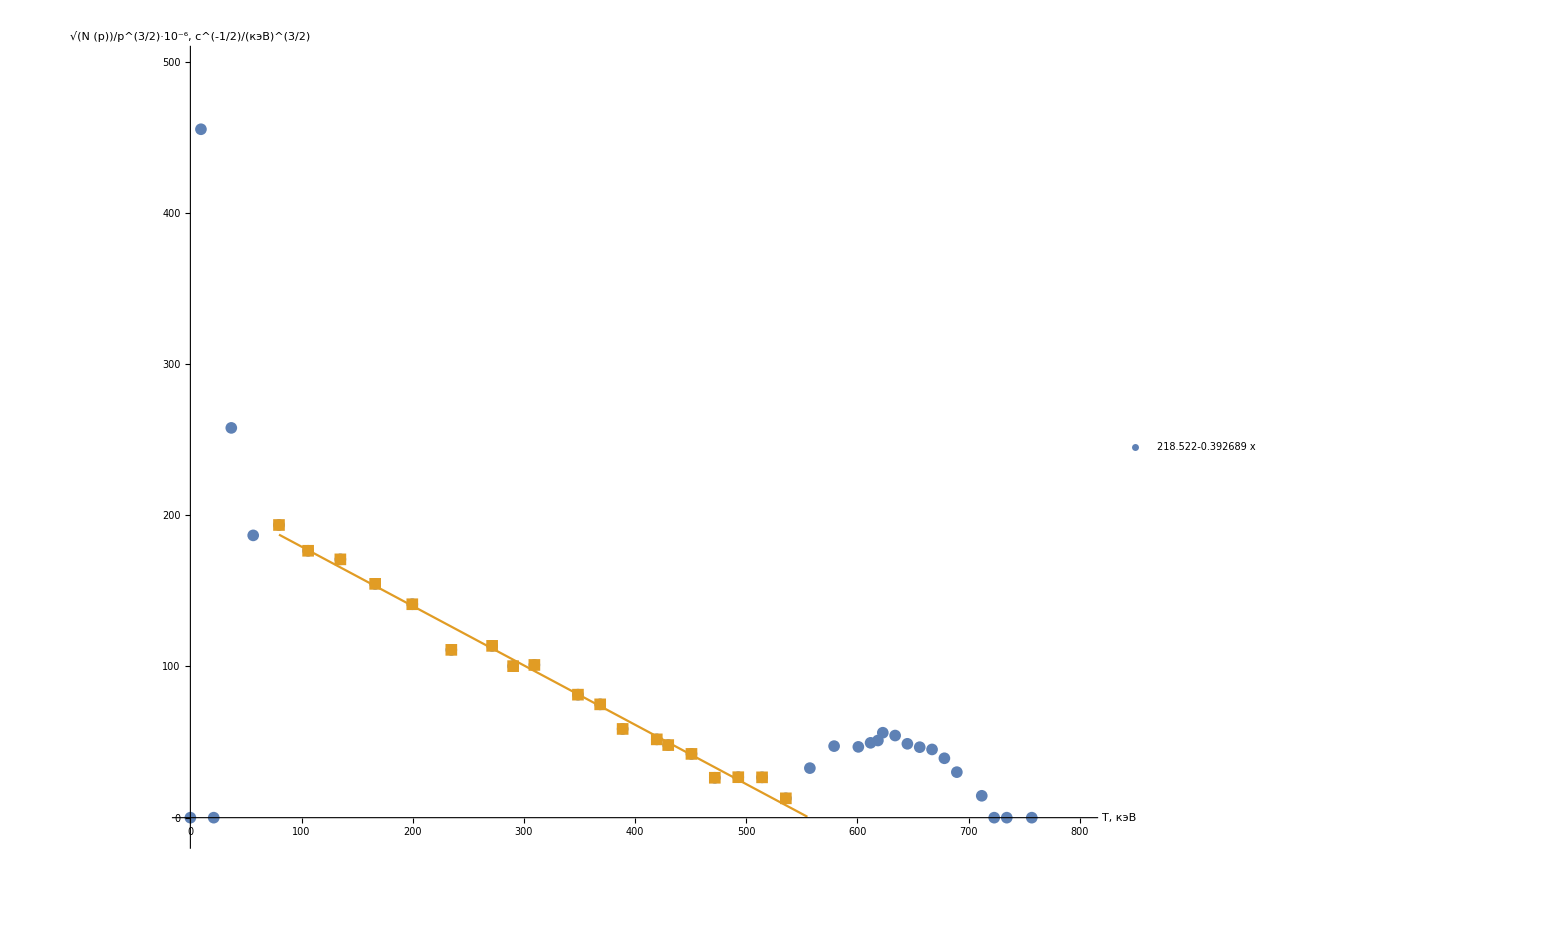

```mathematica
Show[
ListPlot[
{dataset2,datasetline},
PlotRange-> {{-0.1,800},{-10, 500}},
Ticks-> {Range[-1000,1000, 50],Range[-1000,1000, 100]},
TicksStyle->Directive[Black, 14],
PlotMarkers-> {Automatic, 12},
AxesLabel-> {Style["T, кэВ", Large], Style["√(N (p))/p^(3/2)·10^-6, \n c^(-1/2)/(кэВ)^(3/2)", Large]},
AxesStyle->Directive[Arrowheads[0.02],Black],
ImageSize->1500,
GridLines-> {Range[-1000,1000, 10],Range[-1000,1000, 10]},
LabelStyle->Black,
PlotLegends->Placed[LineLegend[
{Normal@line1},
LegendMarkerSize->15,
LegendFunction->frame,
LabelStyle->{FontSize->18},
LegendLayout->"Column"
],
{Scaled[0.6],Scaled[0.75]}
]
],
Plot[{1000x+3,line1[x]},{x,79.7, 555}]
]
```